# MOT beam balances for network exp.

P. Huft

Beam balance calculation for the free space beams used in Network Node 1. The beam angles lead to a requirement for non-trivial setting of the saturation intensities of each pair of beams.

Warning:  the equations for the forces are derived assuming low intensity/Isat

```mathematica
(*the X,Y beams lie in the XY plane and each makes angle θx with the x axis. the Z beam is in the YZ plane and makes angle θz with the z axis*)
Clear[s,sx,sy,sz,x,y,z]
δ=20/6;
F=s/(1+s+(2(δ+B))^2)-s/(1+s+(2(δ-B))^2);(*s=I/Isat, δ in units γ, B in units ℏγ/μ*)
θx=27π/180;(*the angle between the X/Y beams and the x axis*)
θz=35π/180;(*angle between the Z beam and the z axis*)
Bx = -x/2;
By=-y/2;
Bz=z;
FX= F/.{s->sx,B->Bx Cos[θx]+By Sin[θx]};(*the X beam force*)
FY= F/.{s->sy,B->By Sin[θx]+Bx Cos[θx]};(*the Y beam force*)
FZ = F/.{s->sz,B->Bz Cos[θz]+By Sin[θz]};(*the Z beam force*)
dF=D[F,B]/.B->0;
Fx=FX Cos[θx]+FY Cos[θx];
Fy=FX Sin[θx]+FY Sin[θx]+FZ Sin[θz];
Fz=FZ Cos[θz];
gradFx=D[Fx,x](*/.B->0*);
gradFy=D[Fy,y](*/.B->0*);
gradFz=D[Fz,z](*/.B->0*);
```

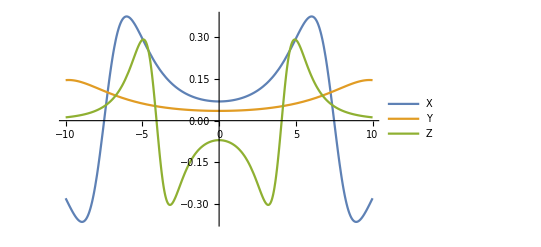

0.0692764

0.0352236

-0.0703187

```mathematica
Clear[sx,sy,sz,x,y,z];
sx=sy=4;
sz=5;
Plot[{gradFx/.{x->r,y->0,z->0},gradFy/.{x->0,y->r,z->0},gradFz/.{x->0,y->0,z->r}},{r,-10,10},PlotRange->All,PlotLegends->{"X","Y","Z"}]
gradFx/.{x->0,y->0,z->0}//N
gradFy/.{x->0,y->0,z->0}//N
gradFz/.{x->0,y->0,z->0}//N
```

```mathematica
Clear[sx,sy,sz];
sx=sy;
gradFx
gradFy
gradFz
```

{{sz→1.93422,sy→0.509231,k→0.331106}}

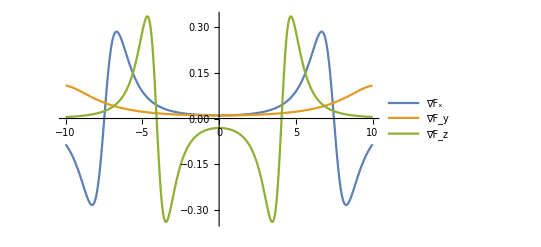

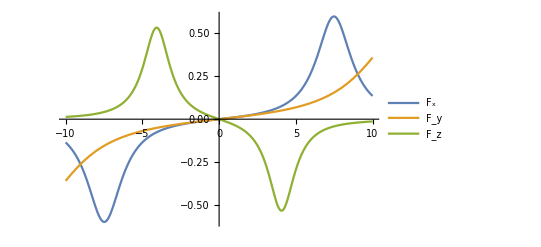

```mathematica
(*solve for intensities which give a symmetric MOT*)
Clear[sx,sy,sz,x,y,z];
x=y=z=0;
sx=sy;
soln=Quiet[NSolve[{gradFy==gradFx,gradFx==-k gradFz},{sz,sy,k},PositiveReals]]
Clear[x,y,z];
Plot[Evaluate[{gradFx/.{x->r,y->0,z->0},gradFy/.{x->0,y->r,z->0},gradFz/.{x->0,y->0,z->r}}/.soln[[1,;;2]]],{r,-10,10},PlotRange->All,PlotLegends->{"∇F_x","∇F_y","∇F_z"}]
Plot[Evaluate[{Fx/.{x->r,y->0,z->0},Fy/.{x->0,y->r,z->0},Fz/.{x->0,y->0,z->r}}/.soln[[1,;;2]]],{r,-10,10},PlotRange->All,PlotLegends->{"F_x","F_y","F_z"}]
```

## misc testing

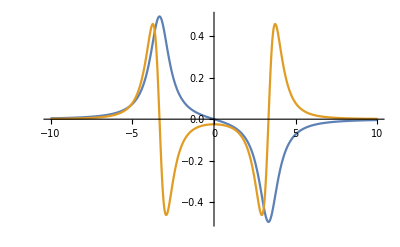

$Aborted

```mathematica
gradF=D[F,B];
Plot[Evaluate[{F,gradF}/.s->1],{B,-10,10},PlotRange->All]
```